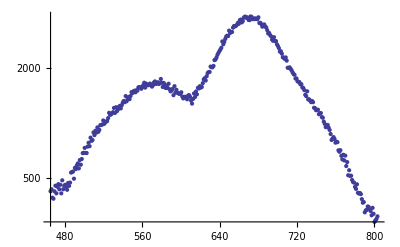

```mathematica
Data = Import["C:\\Users\\Jackson\\Documents\\GitHub\\AdvanceLab\\Gama_Spectroscopy\\data\\Ba-133_gauss_Gainx8.tsv"][[26;;,{2,3}]];
ListLogPlot[Data[[465;;800]]]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a→-20152.4,b→406.557,c→162.749,d→-56.2747,p→45817.1}

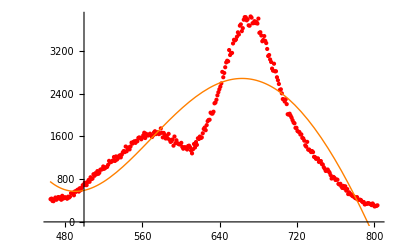

```mathematica
BigPeak=Data[[465;;800]];
FindFit[BigPeak,a E^(-(x-b)^2/(2 c^2))+d x+p,{{a,12000},{b,500},{c,20},d,p},x]
p1 = Plot[a E^(-(x-b)^2/(2 c^2))+d x+p/.%,{x,465,800},PlotStyle->{Orange,Thick}];
p2 = ListPlot[BigPeak,PlotStyle->{Red}];
Show[p2,p1]
```

```mathematica
BigPeak=Data[[465;;800]];
FindFit[BigPeak,Sum[Subscript[a, i] E^(-(x-Subscript[b, i])^2/(2 Subscript[c, i]^2)),{i,3}]+d x+p,{{Subscript[a, 1],3100},{Subscript[b, 1],668},{Subscript[c, 1],26},{Subscript[a, 2],1296},{Subscript[b, 2],570},{Subscript[c, 3],34},{Subscript[a, 3],5000},{Subscript[b, 3],721},{Subscript[c, 2],41},d,p},x]

p1 = Plot[Sum[Subscript[a, i] E^(-(x-Subscript[b, i])^2/(2 Subscript[c, i]^2)),{i,3}]+d x+p/.%,{x,450,800},PlotStyle->{Orange}];
FindFit[BigPeak,Sum[Subscript[a, i] E^(-(x-Subscript[b, i])^2/(2 Subscript[c, i]^2)),{i,3}]+d x+p,{{Subscript[a, 1],3100},{Subscript[b, 1],668},{Subscript[c, 1],26},{Subscript[a, 2],1296},{Subscript[b, 2],570},{Subscript[c, 3],34},{Subscript[a, 3],5000},{Subscript[b, 3],721},{Subscript[c, 2],41},d,p},x];
Do[Subscript[p, i]=Plot[Subscript[a, i] E^(-(x-Subscript[b, i])^2/(2 Subscript[c, i]^2))/.%,{x,450,800},PlotStyle->{Blue,Thin},PlotRange->Full],{i,3}]
p2 = ListPlot[BigPeak,PlotStyle->{Red},AxesLabel -> {"channel","counts"}];
Show[p2,p1,Subscript[p, 1],Subscript[p, 2],Subscript[p, 3]]
```

{a_1→3090.12,b_1→667.974,c_1→26.7598,a_2→1311.96,b_2→570.157,c_3→35.0385,a_3→1016.44,b_3→720.383,c_2→42.0601,d→-0.392022,p→534.725}

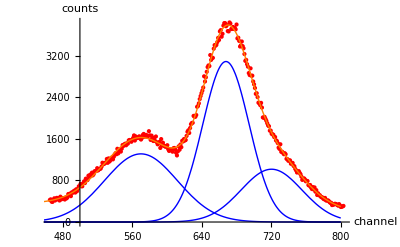
```mathematica
Export["Barium.eps",-Graphics-]
```

Barium.eps

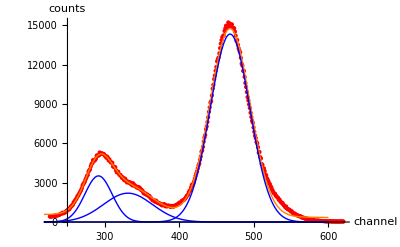
```mathematica
Export["gamaSpeck.png",-Graphics-]
```

gamaSpeck.png